## Simple Reservoir Model

Integrated Model - PP590
Tiago Amorim, RA: 100.675

## Proposed Problem

-Graphics-

-Graphics-

-Graphics-

## Resolution

### Part 1 - Formulation

Assuming black-oil formulation and that there is no free gas in the reservoir, we can simplify this problem to two equations:

-Graphics-   and   -Graphics-

Applying finite differences, using the implicit form for a 1D problem and multiplying by the block volume (V):

```mathematica
∑_(i={i,j,k}) [Subscript[T, p,i+1/2](Subscript[Φ, p,i+1]-Subscript[Φ, p,i])+Subscript[T, p,i-1/2](Subscript[Φ, p,i-1]-Subscript[Φ, p,i])]^(n+1)=(Subscript[V, i]/Δt)[Subscript[(Subscript[ϕS, p]/Subscript[B, p]), i]^(n+1)-Subscript[(Subscript[ϕS, p]/Subscript[B, p]), i]^n]+Subscript[q, p,i]^well
```

Where:
   p is either oil or water
   q^well is in standard conditions 
   i is one of the main flow directions (i,j,k)

The transmissibility in the x-direction is calculated between blocks (equivalent expressions for the other directions):

```mathematica
Subscript[T, p,i+1/2]=Subscript[(Subscript[λ, p](Δx Δy Δz)/Δx^2), i+1/2]=Subscript[(k Subscript[kr, p]/(Subscript[B, p] Subscript[μ, p])(Δx Δy Δz)/Δx^2), i+1/2]=Subscript[((k A)/Δx), i+1/2] Subscript[(1/(Subscript[B, p] Subscript[μ, p])), i+1/2] Subscript[kr, p,i+1/2]
Subscript[((Subscript[k, i] A)/Δx), i+1/2]=Subscript[A, i+1/2]/((Subscript[x, i+1]-Subscript[x, i+1/2])/Subscript[k, i,i+1]+(Subscript[x, i+1/2]-Subscript[x, i])/Subscript[k, i,i])
```

The first part is related to the reservoir characteristics:

```mathematica
Subscript[((Subscript[k, i] A)/Δx), i+1/2]=Subscript[A, i+1/2]/((Subscript[x, i+1]-Subscript[x, i+1/2])/Subscript[k, i,i+1]+(Subscript[x, i+1/2]-Subscript[x, i])/Subscript[k, i,i])
```

Where:
   x_(i+1/2)-x_i is the distance in i direction between the cell center of cells i and the interface between cells i + i+1
   A_(i+1/2) is the flow area in common between cells i and i+1

The second part is a function of pressure:

```mathematica
Subscript[(1/(Subscript[B, p] Subscript[μ, p])), i+1/2]=(Subscript[(1/(Subscript[B, p] Subscript[μ, p])), i]+Subscript[(1/(Subscript[B, p] Subscript[μ, p])), i+1])/2
```

The third part is a function of saturation and equal to the value in the upstream block (larger pressure):

```mathematica
Subscript[kr, p,i+1/2]=Subscript[kr, p,"upstream"]
```

Given that for the proposed problem:
   Φ_(p,i)= P_(p,i) (no vertical displacement)
   P_o = P_w=P (no capillary pressure)
   S_o=1-S_w (no free gas)
   B_o,B_w, μ_o,μ_w, k, Δx, Δy, Δz, V are constants
   1-D problem, in the x direction
   Flow is from the injector (i=1) to the producer (i=3)
The transmissibility becomes:

```mathematica
Subscript[T, p,i+1/2]=(k Δy Δz)/Δx 1/(Subscript[B, p] Subscript[μ, p])Subscript[kr, p,i]
```

The formulation reduces to:

```mathematica
[Subscript[T, p,i+1/2](Subscript[P, i+1]-Subscript[P, i])+Subscript[T, p,i-1/2](Subscript[P, i-1]-Subscript[P, i])]^(n+1)=ΔxΔyΔz/Δt(ϕ/Subscript[B, p])[Subscript[S, p,i]^(n+1)-Subscript[S, p,i]^n]+Subscript[q, p,i]^well
```

```mathematica
(k Δy Δz)/Δx((1/(Subscript[B, p] Subscript[μ, p]))[Subscript[kr, p,i](Subscript[P, i+1]-Subscript[P, i])+Subscript[kr, p,i-1](Subscript[P, i-1]-Subscript[P, i])])^(n+1)=ΔxΔyΔz/Δt(ϕ/Subscript[B, p])[Subscript[S, p,i]^(n+1)-Subscript[S, p,i]^n]+Subscript[q, p,i]^well
```

Which can be write in as a f(x)=0 problem:

```mathematica
(k Δy Δz)/Δx((1/(Subscript[B, p] Subscript[μ, p]))[Subscript[kr, p,i] Subscript[P, i+1]])^(n+1)-(k Δy Δz)/Δx((1/(Subscript[B, p] Subscript[μ, p]))[(Subscript[kr, p,i]+Subscript[kr, p,i-1])Subscript[P, i]])^(n+1)+(k Δy Δz)/Δx((1/(Subscript[B, p] Subscript[μ, p]))[Subscript[kr, p,i-1] Subscript[P, i-1]])^(n+1)
-ΔxΔyΔz/Δt ϕ/Subscript[B, p] Subscript[S, p,i]^(n+1)+ΔxΔyΔz/Δt ϕ/Subscript[B, p] Subscript[S, p,i]^n-Subscript[q, p,i]^well=0
```

Where:
   (S_(p,i))^0 is known
   P_i^0 is known

Problem variables:
   (S_(p,i))^n and P_i^n, with n={1,2,...,n_(t end)}
Important to remember that:
   kr_p=f(S_p)

### Part 2 - Wells

For cell i=1 there is an injector with constant water injection rate:

```mathematica
Subscript[q, w,1]^well=Subscript[Q, w]
Subscript[q, o,1]^well=0
```

Cell i=2 has no wells:

```mathematica
Subscript[q, w,2]^well=0
Subscript[q, o,2]^well=0
```

Cell i=3 has a producer with constant bottom-hole pressure (p_wf):

```mathematica
Subscript[q, w,3]^well=WI Subscript[kr, w]/(Subscript[B, w] Subscript[μ, w])(Subscript[P, wf]-Subscript[P, 3])
Subscript[q, o,3]^well=WI Subscript[kr, o]/(Subscript[B, o] Subscript[μ, o])(Subscript[P, wf]-Subscript[P, 3])
```

With Δx=Δy and k_x=k_y=k:

```mathematica
WI=(2π k Δz)/(ln(Subscript[r, e]/Subscript[r, w])+S)=(2π k Δz)/(ln((0.208Δx)/Subscript[r, w]))
```

### Part 3 - System of equations

Some additional constants to simplify the notation:

```mathematica
(k Δy Δz)/Δx 1/(Subscript[B, p] Subscript[μ, p])=Subscript[α, p]
```

```mathematica
ΔxΔyΔz/Δt ϕ/Subscript[B, p]=β
```

```mathematica
WI 1/(Subscript[B, p] Subscript[μ, p])=Subscript[τ, p]
```

Thus, the main formula becomes:

```mathematica
(Subscript[α, p][Subscript[kr, p,i] Subscript[P, i+1]])^(n+1)-(Subscript[α, p][(Subscript[kr, p,i]+Subscript[kr, p,i-1])Subscript[P, i]])^(n+1)+(Subscript[α, p][Subscript[kr, p,i-1] Subscript[P, i-1]])^(n+1)-Subscript[β, p] Subscript[S, p,i]^(n+1)+Subscript[β, p] Subscript[S, p,i]^n-Subscript[q, p,i]^well=0
```

Plugging everything together:

```mathematica
(Subscript[α, o][Subscript[kr, o,1] Subscript[P, 2]])^(n+1)-(Subscript[α, o][Subscript[kr, o,1] Subscript[P, 1]])^(n+1)+Subscript[β, o] Subscript[S, w,1]^(n+1)-Subscript[β, o] Subscript[S, w,1]^n=0
(Subscript[α, w][Subscript[kr, w,1] Subscript[P, 2]])^(n+1)-(Subscript[α, w][Subscript[kr, w,1] Subscript[P, 1]])^(n+1)-Subscript[β, w] Subscript[S, w,1]^(n+1)+Subscript[β, w] Subscript[S, w,1]^n-Subscript[Q, w]=0
```

```mathematica
(Subscript[α, o][Subscript[kr, o,2] Subscript[P, 3]])^(n+1)-(Subscript[α, o][(Subscript[kr, o,2]+Subscript[kr, o,1])Subscript[P, 2]])^(n+1)+(Subscript[α, o][Subscript[kr, o,1] Subscript[P, 1]])^(n+1)+Subscript[β, o] Subscript[S, w,2]^(n+1)-Subscript[β, o] Subscript[S, w,2]^n=0
(Subscript[α, w][Subscript[kr, w,2] Subscript[P, 3]])^(n+1)-(Subscript[α, w][(Subscript[kr, w,2]+Subscript[kr, w,1])Subscript[P, 2]])^(n+1)+(Subscript[α, w][Subscript[kr, w,1] Subscript[P, 1]])^(n+1)-Subscript[β, w] Subscript[S, w,2]^(n+1)+Subscript[β, w] Subscript[S, w,2]^n=0
```

```mathematica
-(Subscript[α, o][Subscript[kr, o,2] Subscript[P, 3]])^(n+1)+(Subscript[α, o][Subscript[kr, o,2] Subscript[P, 2]])^(n+1)+Subscript[β, o] Subscript[S, w,3]^(n+1)-Subscript[β, o] Subscript[S, w,3]^n-(Subscript[τ, o][Subscript[kr, o,3]])^(n+1)Subscript[P, wf]+(Subscript[τ, o][Subscript[kr, o,3] Subscript[P, 3]])^(n+1)=0
-(Subscript[α, w][Subscript[kr, w,2] Subscript[P, 3]])^(n+1)+(Subscript[α, w][Subscript[kr, w,2] Subscript[P, 2]])^(n+1)-Subscript[β, w] Subscript[S, w,3]^(n+1)+Subscript[β, w] Subscript[S, w,3]^n-(Subscript[τ, w][Subscript[kr, w,3]])^(n+1)Subscript[P, wf]+(Subscript[τ, w][Subscript[kr, w,3] Subscript[P, 3]])^(n+1)=0
```

### Part 4 - Newton-Raphson

Since it is not possible to directly solve the system of equations, Newton-Raphson will be employed to search for the answer in each time-step.
Rewriting the problem in matrix form (K x = f):

```mathematica
({{-(Subscript[α, o][Subscript[kr, o,1]])^(n+1), Subscript[β, o], (Subscript[α, o][Subscript[kr, o,1]])^(n+1), 0, 0, 0}, {-(Subscript[α, w][Subscript[kr, w,1]])^(n+1), -Subscript[β, w], (Subscript[α, w][Subscript[kr, w,1]])^(n+1), 0, 0, 0}, {(Subscript[α, o][Subscript[kr, o,1]])^(n+1), 0, -(Subscript[α, o][Subscript[kr, o,2]+Subscript[kr, o,1]])^(n+1), Subscript[β, o], (Subscript[α, o][Subscript[kr, o,2]])^(n+1), 0}, {(Subscript[α, w][Subscript[kr, w,1]])^(n+1), 0, -(Subscript[α, w][Subscript[kr, w,2]+Subscript[kr, w,1]])^(n+1), -Subscript[β, w], (Subscript[α, w][Subscript[kr, w,2]])^(n+1), 0}, {0, 0, (Subscript[α, o][Subscript[kr, o,2]])^(n+1), 0, -(Subscript[α, o][Subscript[kr, o,2]])^(n+1)+(Subscript[τ, o][Subscript[kr, o,3]])^(n+1), Subscript[β, o]}, {0, 0, (Subscript[α, w][Subscript[kr, w,2]])^(n+1), 0, -(Subscript[α, w][Subscript[kr, w,2]])^(n+1)+(Subscript[δτ, w][Subscript[kr, w,3]])^(n+1), -Subscript[β, w]}})({{Subscript[P, 1]^(n+1)}, {Subscript[S, w,1]^(n+1)}, {Subscript[P, 2]^(n+1)}, {Subscript[S, w,2]^(n+1)}, {Subscript[P, 3]^(n+1)}, {Subscript[S, w,3]^(n+1)}})=({{Subscript[β, o] Subscript[S, w,1]^n}, {-Subscript[β, w] Subscript[S, w,1]^n+Subscript[Q, w]}, {Subscript[β, o] Subscript[S, w,2]^n}, {-Subscript[β, w] Subscript[S, w,2]^n}, {Subscript[β, o] Subscript[S, w,3]^n+(Subscript[τ, o][Subscript[kr, o,3]])^(n+1)Subscript[P, wf]}, {-Subscript[β, w] Subscript[S, w,3]^n+(Subscript[τ, w][Subscript[kr, w,3]])^(n+1)Subscript[P, wf]}})
```

To use NR it is needed the Jacobian of R = (K x - f):

```mathematica
J=({{-(Subscript[α, o][Subscript[kr, o,1]])^(n+1), Subscript[β, o]+Subscript[α, o] (Subscript[P, 2]^(n+1)-Subscript[P, 1]^(n+1))Subscript[δkr, o,1]/Subscript[δS, w,1], (Subscript[α, o][Subscript[kr, o,1]])^(n+1), 0, 0, 0}, {-(Subscript[α, w][Subscript[kr, w,1]])^(n+1), -Subscript[β, w]+Subscript[α, w] (Subscript[P, 2]^(n+1)-Subscript[P, 1]^(n+1))Subscript[δkr, w,1]/Subscript[δS, w,1], (Subscript[α, w][Subscript[kr, w,1]])^(n+1), 0, 0, 0}, {(Subscript[α, o][Subscript[kr, o,1]])^(n+1), Subscript[α, o] (Subscript[P, 2]^(n+1)-Subscript[P, 1]^(n+1))Subscript[δkr, o,1]/Subscript[δS, w,1], -(Subscript[α, o][Subscript[kr, o,2]+Subscript[kr, o,1]])^(n+1), Subscript[β, o]+Subscript[α, o] (Subscript[P, 3]^(n+1)-Subscript[P, 2]^(n+1))Subscript[δkr, o,2]/Subscript[δS, w,2], (Subscript[α, o][Subscript[kr, o,2]])^(n+1), 0}, {(Subscript[α, w][Subscript[kr, w,1]])^(n+1), Subscript[α, w] (Subscript[P, 2]^(n+1)-Subscript[P, 1]^(n+1))Subscript[δkr, w,1]/Subscript[δS, w,1], -(Subscript[α, w][Subscript[kr, w,2]+Subscript[kr, w,1]])^(n+1), -Subscript[β, w]+Subscript[α, w] (Subscript[P, 3]^(n+1)-Subscript[P, 2]^(n+1))Subscript[δkr, w,2]/Subscript[δS, w,2], (Subscript[α, w][Subscript[kr, w,2]])^(n+1), 0}, {0, 0, (Subscript[α, o][Subscript[kr, o,2]])^(n+1), Subscript[α, o] (Subscript[P, 2]^(n+1)-Subscript[P, 3]^(n+1))Subscript[δkr, o,2]/Subscript[δS, w,2], -(Subscript[α, o][Subscript[kr, o,2]])^(n+1)+(Subscript[τ, o][Subscript[kr, o,3]])^(n+1), Subscript[β, o]+(Subscript[τ, o][Subscript[P, 3]-Subscript[P, wf]])^(n+1)Subscript[δkr, o,3]/Subscript[δS, w,3]}, {0, 0, (Subscript[α, w][Subscript[kr, w,2]])^(n+1), Subscript[α, w] (Subscript[P, 2]^(n+1)-Subscript[P, 3]^(n+1))Subscript[δkr, w,2]/Subscript[δS, w,2], -(Subscript[α, w][Subscript[kr, w,2]])^(n+1)+(Subscript[τ, w][Subscript[kr, w,3]])^(n+1), -Subscript[β, w]+(Subscript[τ, w][Subscript[P, 3]-Subscript[P, wf]])^(n+1)Subscript[δkr, w,3]/Subscript[δS, w,3]}})
```

Newton-Raphson algorithm (with simplified convergence controls):
   Start with the initial state (x^0) and calculate f and an approximation of K.
   Define Δt
   For i=1,...,n
      Make x_0^i=x^(i-1)
      Repeat
         x_(j+1)^i=x_j^i-J^-1(Kx-f)
      Until convergence: ||K x - f|| < ϵ or j=j_max
      if Δ_t P>Δ_t P_max or Δ_t S>Δ_t S_max then
         Δt^new=Δt/2
         Repeat time-step
      else
         Δt^new=1.2 Δt

### Part 5 - Relative Permeability

The provided plot was manually digitalized, and the curves were approximated with known Kr correlations. The major endpoints are:

```mathematica
Swc=0.10;
Swcr=0.20;
Sor=0.16;
Krwmax = 0.63;
Kromax=1.00;
```

The water curve was adjusted to the Corey formulation:

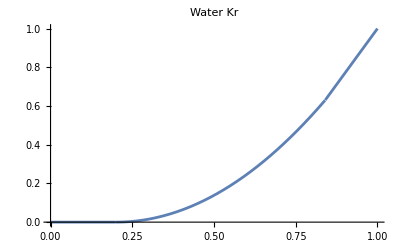

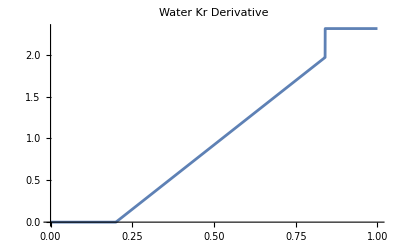

```mathematica
nw=2;
krw=Piecewise[{{0,Sw<Swcr},{Krwmax*Power[(Sw-Swcr)/(1-Swcr-Sor),nw],Sw<=1-Sor},{Krwmax+(1-Krwmax)*(Sw-1+Sor)/Sor,Sw<=1},{1,Sw>1}}];
Plot[krw,{Sw,0,1},PlotLabel->"Water Kr"]
Plot[D[krw,Sw]/.Sw->x,{x,0,1},PlotLabel->"Water Kr Derivative"]
```